# EquilateralTriangle

Represents an equilateral triangle

## Definition

```mathematica
ClearAll[EquilateralTriangle]
EquilateralTriangle::usage="EquilateralTriangle[] represents an equilateral triangle with sides of length 1. EquilateralTriangle[s] represents an equilateral triangle with sides of length s.";
SetAttributes[EquilateralTriangle,{Listable}]
Which[TrueQ[$VersionNumber≥13.3],EquilateralTriangle[Optional[s:(_?(MatchQ[#,x_?RealValuedNumericQ/;x>0]&)|_?(MatchQ[#,x_Symbol/;ValueQ[x]===False]&)),1]]:=SSSTriangle[s,s,s],TrueQ[$VersionNumber<13.3],EquilateralTriangle[Optional[s:(_?(MatchQ[#,x_Real/;x>0]&)|_?(MatchQ[#,x_Symbol/;ValueQ[x]===False]&)),1]]:=SSSTriangle[s,s,s]]
(*EquilateralTriangle[Optional[s:(_?(MatchQ[#,x_?RealValuedNumericQ/;x>0]&)|_?(MatchQ[#,x_Symbol/;ValueQ[x]===False]&)),1]]:=SSSTriangle[s,s,s]*)
EquilateralTriangle[args___]:=Null/;CheckArguments[EquilateralTriangle[args],{1,1}]
```

## Documentation

### Usage

EquilateralTriangle[]

represents an equilateral triangle with sides of length 1.

EquilateralTriangle[s]

represents an equilateral triangle with sides of length s.

### Details & Options

An equilateral triangle means an equal side triangle. An equilateral triangle is an equiangular triangle, where all angles are the same, 60° or π/3 radians.

In an equilateral triangle, many triangle centers coincide in the center.

## Examples

### Basic Examples

A triangle in which all sides are equal is an equilateral triangle:

```mathematica
t=EquilateralTriangle[]
```

Triangle[{{0,0},{1,0},{1/2,(√3)/2}}]

Visualize it:

```mathematica
Region[t]
```

-Graphics-

Find its area:

```mathematica
Area[EquilateralTriangle[s]]
```

1/4 √3 Abs[s]^2

Use Refine to simplify Abs[s] to just s by assuming the side length is an element of the PositiveReals, written :

```mathematica
Refine[1/4 √3 Abs[s]^2,{s∈PositiveReals}]
```

(√3 s^2)/4

The circumcircle of an SSSTrianglepaclet:ref/SSSTriangle can be found using Circumspherepaclet:ref/Circumsphere:

```mathematica
tri=EquilateralTriangle[]
```

Triangle[{{0,0},{1,0},{1/2,(√3)/2}}]

The circumcircle passes through the three corner points:

```mathematica
circ=Circumsphere[First@tri]
```

Sphere[{1/2,1/(2 √3)},-1/(2 √3)+(√3)/2]

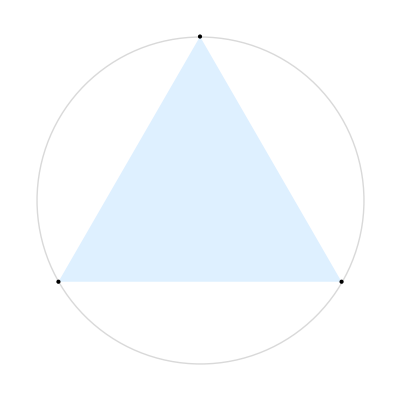

```mathematica
Graphics[{Style[circ,Directive[LightGray]],Style[tri,Directive[LightBlue]],Style[Point[First@tri],Directive[Black]]}]
```

Find the midpoints for each edge of the triangle:

```mathematica
midpts=RegionCentroid[Line[#]]&/@Subsets[First@tri,{2}]
```

{{1/2,0},{1/4,(√3)/4},{3/4,(√3)/4}}

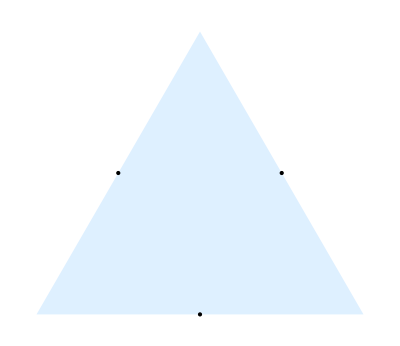

```mathematica
Graphics[{Style[tri,Directive[LightBlue]],Point[midpts]}]
```

The perpendicular bisectors are lines from the circumcenter to the midpoints:

```mathematica
center=First[circ];
bisectors=Line[{center,#}]&/@midpts;
```

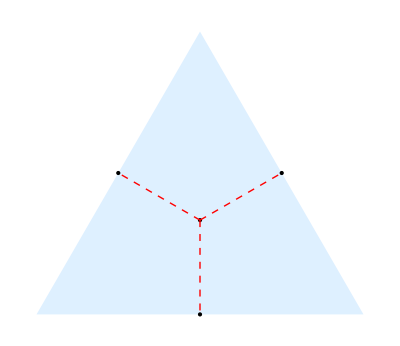

```mathematica
Graphics[{Style[tri,Directive[LightBlue]],Point[center],Point[midpts],Style[bisectors,Directive[Red,Dashed]]}]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

Minimize the perimeter of an SSSTrianglepaclet:ref/SSSTriangle with fixed area:

```mathematica
tri=SSSTriangle[p,q,r];
```

```mathematica
Minimize[{p+q+r,Area[tri]==Sqrt[3]/4&&0<p<=q<=r&&p+q>=r(*the triangle inequality*)},{p,q,r},PositiveReals]
```

{3,{p→1,q→1,r→1}}

As expected, the result is an equilateral triangle:



```mathematica
Graphics[tri/.Last[%]]
```

Find the incenter of an equilateral triangle:

```mathematica
TriangleCenter[EquilateralTriangle[],"Incenter"]
```

{1/2,1/(2 √3)}

```mathematica
TriangleCenter[EquilateralTriangle[s],"Incenter"]
```

{s/2,(√(s^4))/(2 √3 s)}

Calculate the incenter of a triangle:

```mathematica
tri=PolygonCoordinates@EquilateralTriangle[];
pt=TriangleCenter[tri,"Incenter"]
```

{1/2,1/(2 √3)}

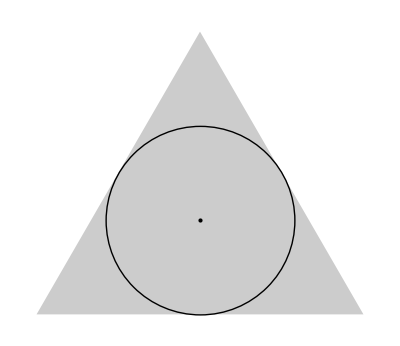

```mathematica
Graphics[{Style[Triangle[tri],Directive[Opacity[0.2]]],Circle[pt,TriangleMeasurement[tri,"Inradius"]],Point[pt]}]
```

Calculate the excenter of a triangle at the specified vertex:

```mathematica
tri=PolygonCoordinates@EquilateralTriangle[];
TriangleCenter[tri,"Excenter"]
```

{1/2,-(√3)/2}

Specify a different vertex:

```mathematica
pt=TriangleCenter[PolygonCoordinates@EquilateralTriangle[],{"Excenter",{0,0}}]
```

{3/2,(√3)/2}

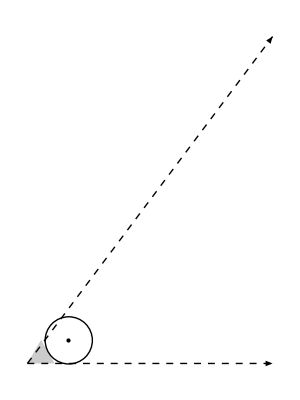

```mathematica
Graphics[{Style[Triangle[tri],Opacity[0.2]],Circle[pt,TriangleMeasurement[tri,{"Exradius",{0,0}}]],Style[Arrow[{{0,0},{9,0}}],Dashed],Style[Arrow[{{0,0},{9,12}}],Dashed],Point[pt]}]
```

Calculate all of the excenters:

```mathematica
TriangleCenter[tri,{"Excenter",All}]
```

{{3/2,(√3)/2},{1/2,-(√3)/2},{-1/2,(√3)/2}}

Calculate the endpoint of an angle bisector:

```mathematica
tri=PolygonCoordinates@EquilateralTriangle[];
pt=TriangleCenter[tri,"AngleBisectingCevianEndpoint"]
```

{1/2,0}

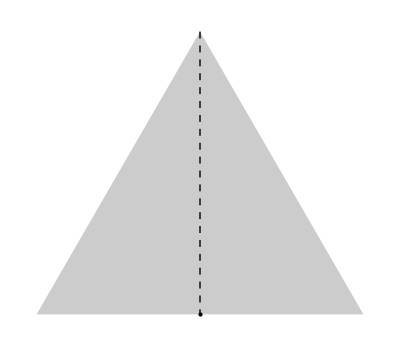

```mathematica
Graphics[{Style[Triangle[tri],Opacity[0.2]],Style[TriangleConstruct[tri,"AngleBisectingCevian"],Dashed],Point[pt]}]
```

Calculate the centroid of a triangle:

```mathematica
tri=PolygonCoordinates@EquilateralTriangle[];
pt=TriangleCenter[tri,"Centroid"]
```

{1/2,1/(2 √3)}

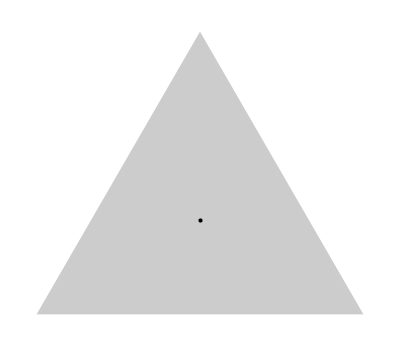

```mathematica
Graphics[{Style[Triangle[tri],Opacity[0.2]],Point[pt]}]
```

Calculate the endpoint of a cevian passing through the orthocenter:

```mathematica
tri=PolygonCoordinates@EquilateralTriangle[];
pt=TriangleCenter[tri,{"CevianEndpoint","Orthocenter"}]
```

{1/2,0}

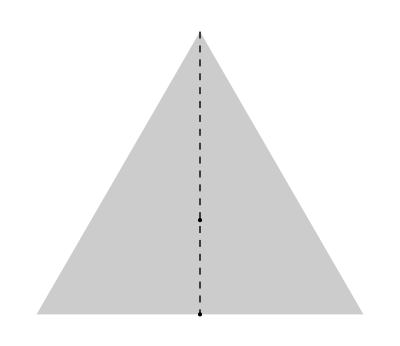

```mathematica
Graphics[{Style[Triangle[tri],Opacity[0.2]],Style[TriangleConstruct[tri,{"Cevian","Orthocenter"}],Dashed],TriangleConstruct[tri,"Orthocenter"],Point[pt]}]
```

Notice the cevian passing through the orthocenter and the angle bisector are the same in an equilateral triangle.

The Euler line passes through the centroid, circumcenter, orthocenter and nine-point center:

```mathematica
tri=PolygonCoordinates@EquilateralTriangle[s];
```

```mathematica
{TriangleCenter[tri,"Centroid"],TriangleCenter[tri,"Circumcenter"],TriangleCenter[tri,"Orthocenter"],TriangleCenter[tri,"NinePointCenter"]}
```

{{s/2,(√(s^4))/(2 √3 s)},{s/2,(√(s^4))/(2 √3 s)},{s/2,(√(s^4))/(2 √3 s)},{s/2,(√(s^4))/(2 √3 s)}}

The centroid, the circumcenter, the orthocenter and the nine-point center are all the same in any equilateral triangle:

```mathematica
SameQ@@{TriangleCenter[tri,"Centroid"],TriangleCenter[tri,"Circumcenter"],TriangleCenter[tri,"Orthocenter"],TriangleCenter[tri,"NinePointCenter"]}
```

True

Make a dataset of equilateral triangles of different sizes:

```mathematica
Dataset@Table[AssociationThread[{"triangle","area","centroid","moment-of-inertia","perimeter"}->({#,{Area[#]},RegionCentroid[#],MomentOfInertia[#],Perimeter[#]})]&[EquilateralTriangle[n]],{n,1,5,1}]
```

-Graphics-

The function is Listable. I'm not sure is this is a good idea because Graphics definitely isn't Listable. It could be helpful for generating large collections of equilateral triangles, like in the example below with 40 randomly colored equilateral triangles.:

```mathematica
EquilateralTriangle[{2,3,5}]
```

{Triangle[{{0,0},{2,0},{1,√3}}],Triangle[{{0,0},{3,0},{3/2,(3 √3)/2}}],Triangle[{{0,0},{5,0},{5/2,(5 √3)/2}}]}

Make an equilateral triangle with a side length of the golden ratio:

```mathematica
EquilateralTriangle[GoldenRatio]
```

Triangle[{{0,0},{GoldenRatio,0},{1/4 (1+√5),1/4 √3 (1+√5)}}]

Make a region:

```mathematica
Region[EquilateralTriangle[GoldenRatio]]
```

-Graphics-

Make a graphic:

```mathematica
Graphics[EquilateralTriangle[GoldenRatio]]
```

-Graphics-

Find the centroid exactly and numerically:

```mathematica
RegionCentroid[EquilateralTriangle[GoldenRatio]]
```

{1/3 (1/4 (1+√5)+GoldenRatio),(1+√5)/(4 √3)}

```mathematica
ResourceFunction["ReadableForm"]@N[RegionCentroid[EquilateralTriangle[GoldenRatio]]]
```

{ 0.8090169943749475, 0.46708617948135794 }

Find the moment of inertia exactly and numerically:

```mathematica
MomentOfInertia[EquilateralTriangle[GoldenRatio]]
```

{{(1+√5)^4/(512 √3),0},{0,(1+√5)^4/(512 √3)}}

```mathematica
ResourceFunction["ReadableForm"][N@MomentOfInertia[EquilateralTriangle[GoldenRatio]]]
```

{ { 0.12366305047710623, 0. }, { 0., 0.12366305047710623 } }

Find the region moment:

```mathematica
RegionMoment[EquilateralTriangle[GoldenRatio],{2,2}]
```

1/480 (7+3 √5) (3 √3+√15)

```mathematica
ResourceFunction["ReadableForm"]@N@RegionMoment[EquilateralTriangle[GoldenRatio],{2,2}]
```

0.25900325544124636

Find the perimeter:

```mathematica
FullSimplify@Perimeter[EquilateralTriangle[GoldenRatio]]
```

3/2 (1+√5)

```mathematica
ResourceFunction["ReadableForm"]@N@FullSimplify@Perimeter[EquilateralTriangle[GoldenRatio]]
```

4.854101966249685

### Properties and Relations

### Possible Issues

### Neat Examples

Random equilateral triangles with 0.5 opacity to allow seeing triangles in the background:

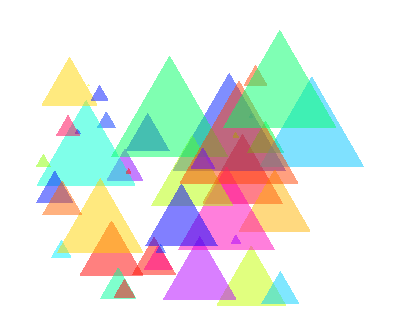

```mathematica
Graphics[Table[{RandomColor[Hue[_,1,1,0.5],ColorSpace->"HSB"],Translate[EquilateralTriangle[RandomReal[5]],RandomReal[10,{2}]]},40]]
```

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Triangles

Geometry

Planar geometry

Polygons

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SSSTriangle

Triangle

Polygon

### Related Resource Objects

TriangularGridGraph

### Source/Reference Citation

The documentation for SSSTriangle, StadiumShape, and TriangleCenter. I also got help from ChatGPT.

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.